Plotting

No tutorial here, just some examples you can play around with, copy, and modify for your own use.  

HELP: Use F1 on any options you don’t understand.  Refer to the Plot help page or the Options for Graphics tutorial

```mathematica
ClearAll["Global`*"]
```

Basic Example Plots

Some things to notice:  
- Items in a list must be enclosed in {brackets}
- For plots of more than one function, the PlotStyle option must be a list of lists, where the first list refers to the first function, and so on.

Graph title, labeing axes

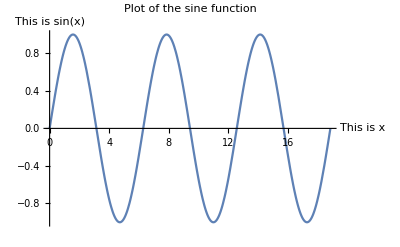

```mathematica
Plot[Sin[x],{x,0,6*Pi},AxesLabel->{"This is x","This is sin(x)"},PlotLabel->"Plot of the sine function"]
```

Gridlines, formatted text & line styles

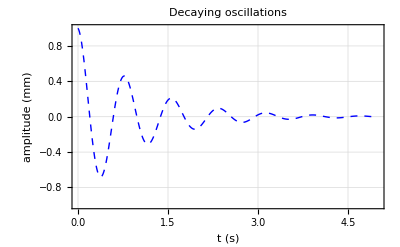

```mathematica
Plot[Cos[8 t] E^-t,{t,0, 5}, PlotRange->{-1,1}, PlotStyle-> {Blue, Thick, Dashed},  GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted], PlotLabel->"Decaying oscillations", Frame->True,FrameLabel -> {"t (s)","amplitude (mm)"},LabelStyle->{Pink,Bold,Larger},AxesOrigin->{0,-1}]
```

Labeling tickmarks

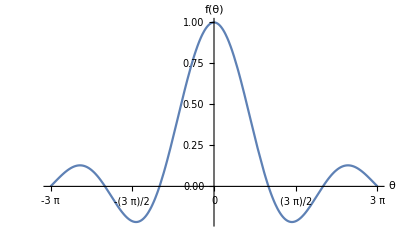

```mathematica
Plot[Sin[x]/x,{x,-3 Pi,3 Pi},Ticks->{Range[-3 Pi,3 Pi,Pi/2],Automatic},AxesLabel->{"θ","f(θ)"}](*choosing a starting, ending, and interval for the x-ticks and automatic values for the y*)
```

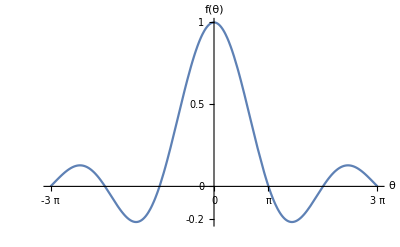

```mathematica
Plot[Sin[x]/x,{x,-3 Pi,3 Pi},Ticks->{{-3 Pi,-Pi,0,Pi/2,Pi,2Pi,3Pi},{-.2,0,.5,1}},AxesLabel->{"θ","f(θ)"}](*choosing specific values for each set of tickmarks; notice they don't have to be equally spaced*)
```

Making separate plots, displaying them together, plotting points

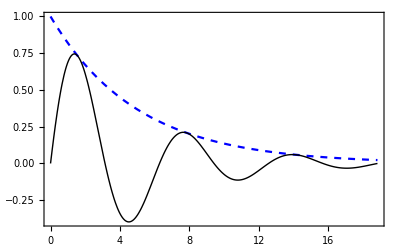

```mathematica
plot1=Plot[Exp[-x/5],{x,0,6 Pi},PlotStyle-> {{Blue, Dashed}}];
plot2=Plot[Sin[x]*Exp[-x/5],{x,0,6 Pi},PlotStyle-> {Black, Thick}];
Show[{plot1,plot2},PlotRange->Automatic,Frame->True]
```

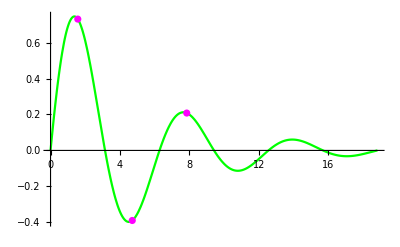

```mathematica
f[x_]=Sin[x]*Exp[-x/5];
plot2=Plot[f[x],{x,0,6 Pi},PlotStyle-> {Green}];
Show[plot2,ListPlot[{{Pi/2,f[Pi/2]},{3 Pi/2,f[3 Pi/2]},{5 Pi/2,f[5 Pi/2]}},PlotStyle-> {Magenta,Thick}]]
```

Plotting points on the complex plane

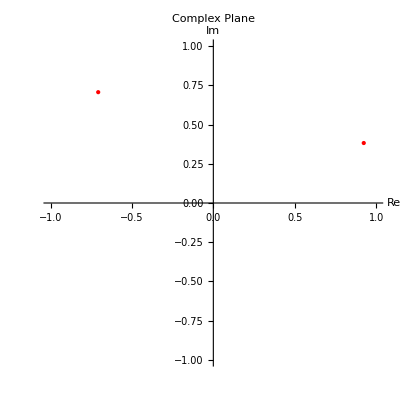

```mathematica
z1=Exp[3 I*Pi/4];
z2=Exp[I*Pi/8];
ListPlot[{{Re[z1],Im[z1]},{Re[z2],Im[z2]}},PlotRange->{{-1,1},{-1,1}},AspectRatio->Automatic,AxesLabel->{"Re","Im"},PlotStyle->{PointSize[Large],Red},PlotLabel->"Complex Plane"]
```

Plotting several functions, excluding asymptotes

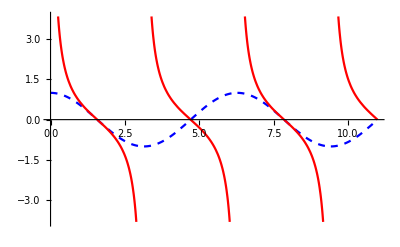

```mathematica
Plot[{Cos[x],Cot[x]},{x,0,3.5*Pi},PlotStyle-> {{Blue, Dashed},{Red}},Exclusions->{{},Pi,2*Pi,3*Pi}](*Nothing excluded from the Cos plot, asymptotes excluded from the Cot plot*)
```

Labeling different functions using PlotLegends and PlotLabels

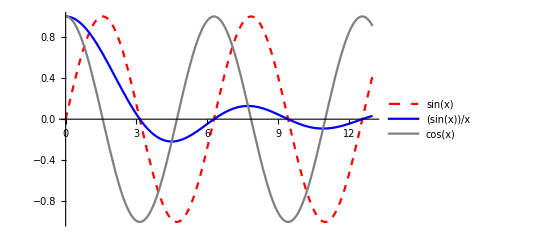

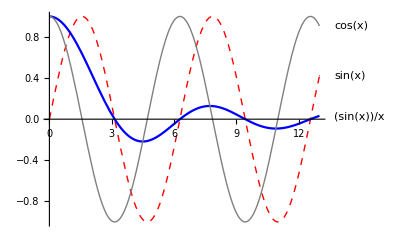

```mathematica
Plot[{Sin[x],Sin[x]/x,Cos[x]},{x,0,13},PlotStyle->{{Red,Thick,Dashed},Blue,{Gray,Thin}},PlotLegends->"Expressions"]
Plot[{Sin[x],Sin[x]/x,Cos[x]},{x,0,13},PlotStyle->{{Red,Thick,Dashed},Blue,{Gray,Thin}},PlotLabels->"Expressions"]
```

Plot frame

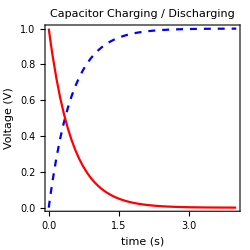

```mathematica
Plot[{1-Exp[-2t],  Exp[-2t]},{t,0, 4}, PlotStyle-> {{Blue, Dashed},{Red}}, Frame->True, PlotLabel->Style["Capacitor Charging / Discharging",FontColor->Gray,FontSlant->Italic,FontWeight->Bold, FontSize->15,FontFamily->"Times New Roman"],FrameLabel->{Style["time (s)",FontFamily->"Times New Roman"], Style["Voltage (V)", FontFamily->"Times New Roman"]} , ImageSize->250 , AspectRatio->1]
```

Semi-log and log-log plots

Notice that the “Log” in the plot calls refers to a base-10 log.  This is different from the function Log, which is the base-e log, what we usually call “ln”

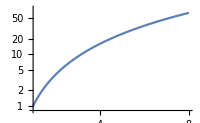

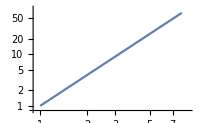

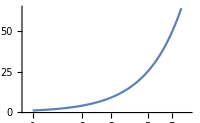

```mathematica
LogPlot[t^2,{t,1, 8},PlotRange->All,ImageSize->200](*x-axis linear, y-axis log*)
LogLogPlot[t^2,{t,1, 8},PlotRange->All,ImageSize->200](*x-axis log, y-axis log*)
LogLinearPlot[t^2,{t,1, 8},PlotRange->All,ImageSize->200](*x-axis log, y-axis linear*)
```

#### Animating & Manipulating curves

Notice: Make sure you put Plot options inside the [plot command] and not the Manipulate or Animate command, & vice versa

Changing plot parameters interactively using Manipulate

```mathematica
Manipulate[Plot[Sin[m x],{x,0,5*Pi}],{m,0,6,1}]
```

Of the settings which control the adjustable parameter (“m”), the last is optional, and specifies the step size.  In this example setting the step size to 1 restricts m to being an integer.
Clicking “+“ to the right of the m parameter setting brings up more controls; play around with these to see how you can animate the plot.

Manipulate with two parameters, automatic animation

A Gaussian distribution

```mathematica
Manipulate[Plot[1/(2*Pi*sigma)* E^((-1/2)*(x-b)^2/sigma^2),{x,-12, 12},PlotRange->{0,.5}], {b,-8,8},{sigma,.001,5}]
```

Manipulate is tremendously useful, with one significant downside: the only parameters Manipulate sees are the ones explicitly inside the Manipulate function.  So you can’t define a function elsewhere, then try to plot it via Manipulate.

Use the control buttons to control various aspects of the animation below:

```mathematica
Animate[Plot[1/(2*Pi*sigma)* E^((-1/2)*(x-b)^2/sigma^2),{x,-12, 12},PlotRange->{0,.5}], {b,-8,8},{sigma,.001,5},AnimationRate->2, AnimationDirection->ForwardBackward]
```

Animate

```mathematica
Animate[Plot[Sin[5 x - 2 t],{x,0,10}, Background->LightBlue],{t,0,10},AnimationRunning->False]
```

Set the PlotRange option to keep the y-axis from jumping around.  Look at this example of an animation without and with PlotRange to see how it affects your understanding of the function:

```mathematica
wave[x_,t_]=Sin[5 x - 2 t]+Sin[5 x + 2 t]
Animate[Plot[wave[x,t],{x,0,5} , ImageSize->250],{t,0,10} ]
```

-Sin[2 t-5 x]+Sin[2 t+5 x]

```mathematica
Animate[Plot[wave[x,t],{x,0,5},PlotRange->{-2,2} , ImageSize->250],{t,0,10}]
```

Controlling animations

Use the down-arrow control buttons to change the animation rate and pause the animation, or do this with the options AnimationRate and AnimationRunning

```mathematica
Animate[Plot[wave[x,t],{x,0,5},PlotRange->{-2,2}],{t,0,50},AnimationRate->.2, AnimationRunning->False]
```

Fixing jerky animations
If your animations seem to stutter and jerk, it may be that each numerical value of the expression you’re plotting takes a little too much time - you may encounter this if the expression involves an integration or summation.  Try pulling this calculation OUT of the Animation command so that Mathematica can do as much of it as possible in advance, and doens’t have to repeat the same thing every single time it calculates a new frame of the animation.

Sampling

Mathematica plots an expression by sampling it at some finite number of points and then connecting the dots.  Rapidly-oscillating functions may not be sampled with enough points to create smooth graphs.
- Plotpoints → p: Start with p evenly-spaced points.  In these examples, p=10
- MaxRecursion → n: Increase the plotted points by a factor of n^2, adding more points around sharp features where the function changes most rapidly.  In these examples, n takes on values 0 to 5
- Mesh → All: Show the sampled points

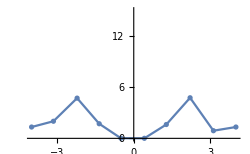

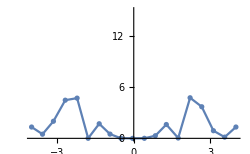

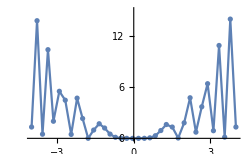

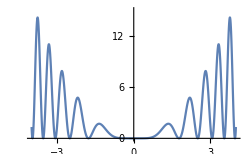

```mathematica
fnA=(Sin[x^2]*x)^2;
Plot[fnA,{x,-4,4} , ImageSize->250,PlotRange->{0,15},Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->0]
Plot[fnA,{x,-4,4} , ImageSize->250,PlotRange->{0,15},Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->1]
Plot[fnA,{x,-4,4} , ImageSize->250,PlotRange->{0,15},Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->2]
Plot[fnA,{x,-4,4} , ImageSize->250,PlotRange->{0,15},PlotPoints->5,MaxRecursion->10]
```

#### Filling

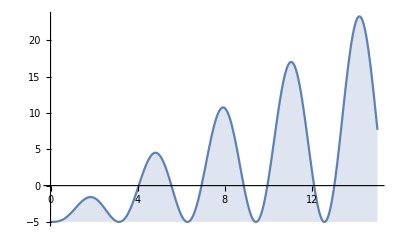

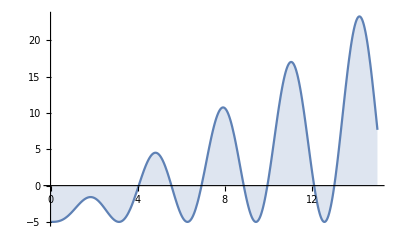

```mathematica
Plot[2 x Sin[x]^2-5,{x,0,15},Filling->Bottom]
Plot[2 x Sin[x]^2-5,{x,0,15},Filling->Axis]
```

Filling between the region of the first and second curves:

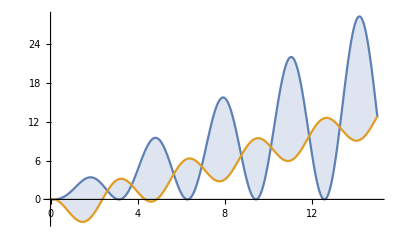

```mathematica
Plot[{2x Sin[x]^2,x -5Sin[x]^2},{x,0,15},Filling->{1-> {2}}]
```

#### Parametric plots

A parametric plot is a plot of one function of a variable versus another function of the same variable, over a range in values of that variable.  It’s a 1D curve (described by a single variable), which exists in 2 or 3 dimensions.

Two functions of a variable plotted against that variable - this is NOT a parametric plot

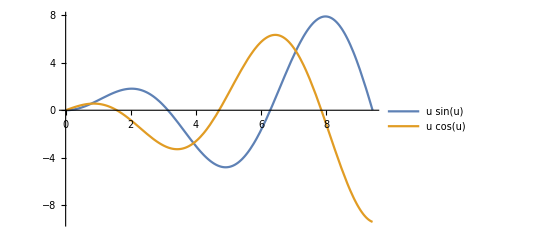

```mathematica
Plot[{u*Sin[u],u*Cos[u]},{u,0,3Pi}, PlotLegends->"Expressions"]
```

Now look at a plot which IS a parametric plot of the same functions:

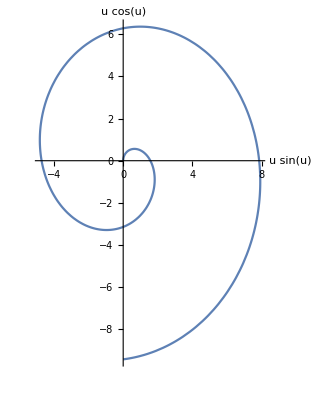

```mathematica
ParametricPlot[{u*Sin[u],u* Cos[u]},{u,0,3Pi},AxesLabel->{u*Sin[u],u* Cos[u]}]
```

See also: ParametricPlot3D, PolarPlot, RevolutionPlot3D, SphericalPlot3D

Visualizing functions of 2 variables: 3D, Contour, Density Plots

Click & drag on the image handles

```mathematica
Plot3D[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

Plot lines of constant intervals of x, y, or z using MeshFunctions.  The default MeshFunction rule (which creates the plot above) is {#1&,#2&}.  “Mesh” controls the density of the mesh lines.

```mathematica
Plot3D[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},MeshFunctions->{#1&},Mesh->7,PlotRange->All] 
Plot3D[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},MeshFunctions->{#2&},Mesh->7,PlotRange->All] 
Plot3D[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},MeshFunctions->{#3&},Mesh->7,PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

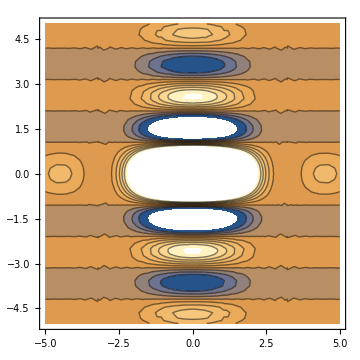

-Graphics-

```mathematica
ContourPlot[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},ImageSize->Medium](*default is fast but could stand better resolution, so...*)
ContourPlot[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},PlotPoints->100,ImageSize->Medium]
```

```mathematica
ContourPlot[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},Contours->50,ImageSize->Medium]
```

-Graphics-

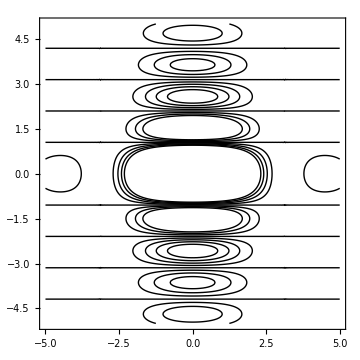

```mathematica
ContourPlot[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},PlotPoints->100,ImageSize->Medium,ContourShading->None] (* just contour lines, no shading *)
```

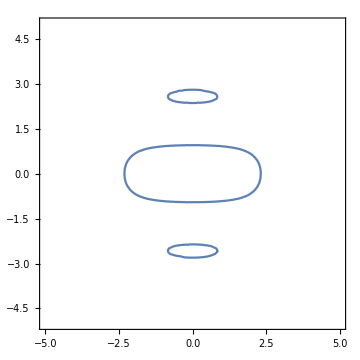

```mathematica
ContourPlot[Sinc[x] ^2 Sinc[3 y]==0.1,{x,-5,5},{y,-5,5},ImageSize->Medium](*Note double equals signs; picks out just one particular contour line*)
```

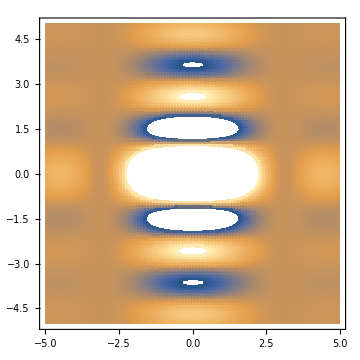

```mathematica
DensityPlot[Sinc[x] ^2 Sinc[3 y],{x,-5,5},{y,-5,5},PlotPoints->100,ImageSize->Medium]
```

Vector Plots in 2D & 3D

For these plots decreasing the number of VectorPoints may give better curves

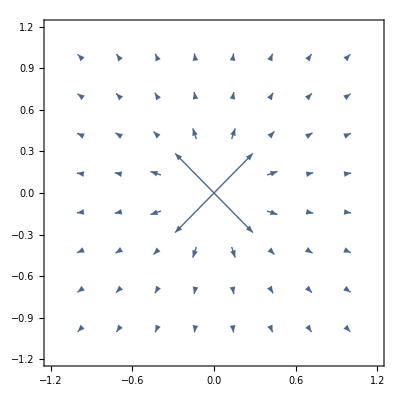

```mathematica
VectorPlot[{x/(x^2+y^2)^1.5,y/(x^2+y^2)^1.5},{x,-1,1},{y,-1,1},VectorPoints->8]
```

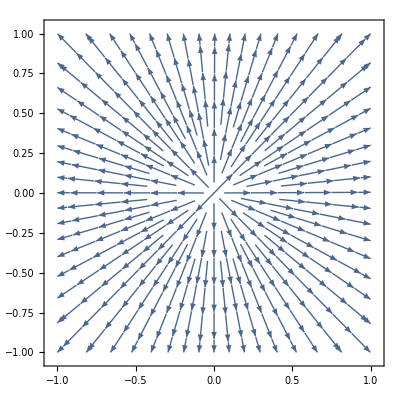

```mathematica
StreamPlot[{x/(x^2+y^2)^1.5,y/(x^2+y^2)^1.5},{x,-1,1},{y,-1,1}] (*Note NO VectorPoints option*)
```

```mathematica
VectorPlot3D[{x/(x^2+y^2+z^2)^1.5,y/(x^2+y^2+z^2)^1.5,z/(x^2+y^2+z^2)^1.5},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->10]
```

-Graphics3D-

This function has a curl directed along the axis -î -ĵ-k̂ , and the initial viewpoint is chosen to highlight this.  Grab the cube & rotate it to better understand the perspective

```mathematica
fn={y,z,x}
VectorPlot3D[fn,{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},AxesLabel->{"x","y","z"},VectorScale->Medium,BoxRatios->Automatic,VectorColorFunction->Hue,ViewPoint->{1000,1000,1000}]
```

{y,z,x}

-Graphics3D-

## Combining plot types

This shows the function h and the vector field grad h

1/5 (x^2+y^2)

{(2 x)/5,(2 y)/5}

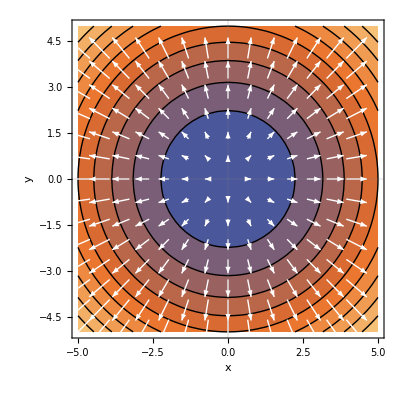

```mathematica
h=1/5(x^2+y^2)
gradh=Grad[h,{x,y}]
vplot=VectorPlot[gradh,{x,-5,5},{y,-5,5},AxesLabel->{"x","y"},VectorScale->Medium,VectorStyle->White];
cplot=ContourPlot[h,{x,-5,5},{y,-5,5},AxesLabel->{"x","y"},PlotTheme->"Scientific"];
Show[{cplot,vplot}]
```

This shows the vector function “fn”, a hemisphere centered on the origin, and the plane z = 0

```mathematica
fn={x,y,z};
plot1=VectorPlot3D[fn,{x,-1.1,1.1},{y,-1.1,1.1},{z,-0.1,1.1},AxesLabel->{"x","y","z"},VectorScale->Medium,BoxRatios->Automatic,VectorColorFunction->Hue];
plot2=SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π}];plot3=ContourPlot3D[z==0,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{x,y,z},ContourStyle->Directive[Orange,Opacity[0.5]]];
Show[{plot1,plot2,plot3}]
```

{x,y,z}

-Graphics3D-

The in-class group work for finding the divergence and using the divergence theorem.  Contains the vector field combined with a plane along z=0 and three semi-transparent shapes embedded in the field.

```mathematica
fn={x^2,y^2,0};
plot1=VectorPlot3D[fn,{x,-2,2},{y,-2,2},{z,-.5,.5},AxesLabel->{"x","y","z"},VectorScale->Small,BoxRatios->Automatic, VectorPoints->{20,20,2}];
plot2=Graphics3D[{Yellow,Opacity[0.5],Cuboid[{.9,1,-.25},{1.7,1.5,.25}],Blue,Cuboid[{-1.9,-.25,-.25},{-1.1,.25,.25}],Red,Sphere[{1.6,-1.6,0},.3]}];plot3=ContourPlot3D[z==0,{x,-2,2},{y,-2,2},{z,-.5,.5},AxesLabel->{x,y,z},ContourStyle->Directive[Orange,Opacity[0.8]],Mesh->None];
Show[{plot1,plot2,plot3}]
```

-Graphics3D-